Зададим данную функцию и построим ее график

```mathematica
f[x_]:=Exp[x]*Cos[2*x]-Sin[3*x];
a=0;
b=Pi;
```

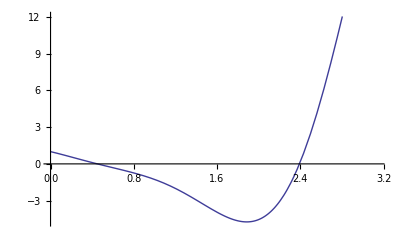

```mathematica
G=Plot[f[x],{x,a,b}]
```

Зададим разбиение отрезка и построим таблично заданную функцию

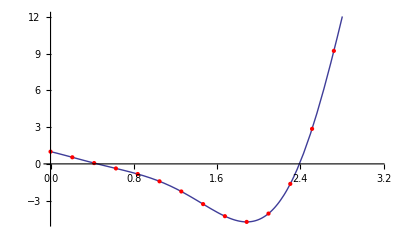

```mathematica
n=15;
h=(b-a)/n;
X=Table[a+(k-1)*h,{k,1,n+1}];
Y=Table[f[X[[k]]],{k,1,n+1}];
XY=Table[{X[[k]],Y[[k]]},{k,1,n+1}];
G1=ListPlot[XY,PlotStyle->Red];
Show[G,G1]
```

Построим многочлен Лагранжа для таблично заданной функции

```mathematica
W=Table[X[[i]]^(n+1-j),{i,1,n+1},{j,1,n}];
W=Transpose[W];
AppendTo[W,Table[1,{i,1,n+1}]];
W=Transpose[W];
A=Inverse[W].Y;
L[x_]:=Sum[A[[i]]*x^(n+1-i),{i,1,n+1}]
```

Построим графики данной функции и многочлена Лагранжа в одной системе координат

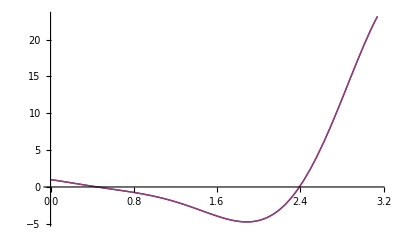

```mathematica
G2=Plot[{f[x],L[x]},{x,a,b}]
```

Оценим погрешность приближения по норме пространства C_[a,b]^2

```mathematica
r=Sqrt[NIntegrate[(f[x]-L[x])^2,{x,a,b}]]
```

0.0000710866

Найдем производную первого порядка для заданной функции и многочлена Лагранжа и построим их графики в одной системе координат

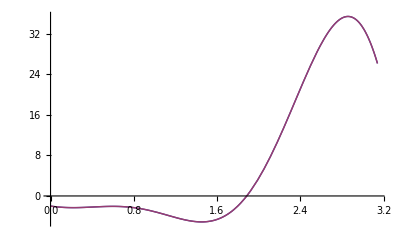

```mathematica
f1[x_]=D[f[x],x];
L1[x_]=D[L[x],x];
G3=Plot[{f1[x],L1[x]},{x,a,b}]
```

Оценим погрешность приближения по норме пространства C_[a,b]^2

```mathematica
r1=Sqrt[NIntegrate[(f1[x]-L1[x])^2,{x,a,b}]]
```

0.000205592

Найдем производную второго порядка для заданной функции и многочлена Лагранжа и построим их графики в одной системе координат

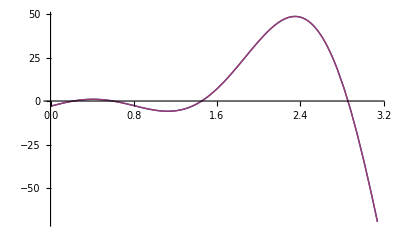

```mathematica
f2[x_]=D[f[x],{x,2}];
L2[x_]=D[L[x],{x,2}];
G4=Plot[{f2[x],L2[x]},{x,a,b}]
```

Оценим погрешность приближения по норме пространства C_[a,b]^2

```mathematica
r2=Sqrt[NIntegrate[(f2[x]-L2[x])^2,{x,a,b}]]
```

0.000918612

Найдем производную третьего порядка для заданной функции и многочлена Лагранжа и построим их графики в одной системе координат

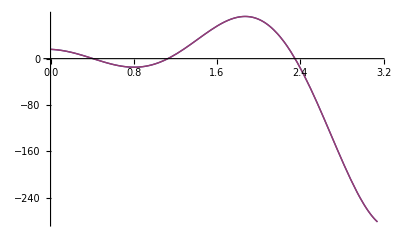

```mathematica
f3[x_]=D[f[x],{x,3}];
L3[x_]=D[L[x],{x,3}];
G5=Plot[{f3[x],L3[x]},{x,a,b}]
```

Оценим погрешность приближения по норме пространства C_[a,b]^2

```mathematica
r3=Sqrt[NIntegrate[(f3[x]-L3[x])^2,{x,a,b}]]
```

0.0193054